# Applying crystal data

2D simulation of reciprocal spacepaclet:MaXrd/tutorial/ApplyingCrystalData#1321285995 | Structure factorspaclet:MaXrd/tutorial/ApplyingCrystalData#188407737
Atomic scattering factorspaclet:MaXrd/tutorial/ApplyingCrystalData#1803163375 | Unit cell transformationpaclet:MaXrd/tutorial/ApplyingCrystalData#624426137

Another tutorial covers the import of crystal data to the format used in this package. In this tutorial we will see a few examples on how to make use of that information.

The package must be loaded:

```mathematica
<<MaXrd`
```

This package comes with many convenient functions that utilises the stored crystal data. They can mainly be divided into two categories: those used to extract data and those used for calculations.

GetAtomicScatteringFactors† | returns f+f'+ⅈ f'' for each elements of the crystal
GetCrystalMetric | return the metric G associated with the crystal lattice
GetLatticeParameters | return the lattice parameters associated with the crystal
GetLaueClass | returns the corresponding Laue class of the group/crystal
GetScatteringCrossSection† | returns σ for given elements and wavelength
GetSymmetryData | extract space group information easily
GetSymmetryOperations | returns alle the symmetry operations for a point- or space group
ImportCrystalData | import crystallographic information from cif files

Functions that are mainly used for easy extraction of data.
† denotes functions that use data files located $MaXrdPath ▶ Core ▶ Data.

AttenuationCoefficient | calulate the μ abosrption factor
BraggAngle | calculate the Bragg angle, given λ and hkl
CrystalDensity | calculate theoretical value for the density
DarwinWidth‡ | calculate the Darwin width of a given hkl
ExtinctionLength‡ | calculate the extinction (Pendellösung) distance of a given hkl
ReciprocalSpaceSimulation | simulate the reflections (nodes) of a plane in reciprocal space
StructureFactor | calculate the structure factor F(hkl)
UnitCellTransformation | transform among alternative unit cell representations

Functions in the package which can operate on data in $CrystalDatapaclet:MaXrd/ref/$CrystalData, $PointGroupspaclet:MaXrd/ref/$PointGroups or $SpaceGroupspaclet:MaXrd/ref/$SpaceGroups directly to perform calculations.
‡ denotes functions related to dynamical diffraction theory.

## 2D simulation of reciprocal space

With the metric information of a crystal contained in $CrystalDatapaclet:MaXrd/ref/$CrystalData and the function for generating appropriate reflections, ReflectionListpaclet:MaXrd/ref/ReflectionList, one can relatively easily create a function that simulates a section of reciprocal space. ReciprocalSpaceSimulationpaclet:MaXrd/ref/ReciprocalSpaceSimulation is a simple function that does this. We can use RelatedFunctionsGraphpaclet:MaXrd/ref/RelatedFunctionsGraph to check which other package components it is made of:

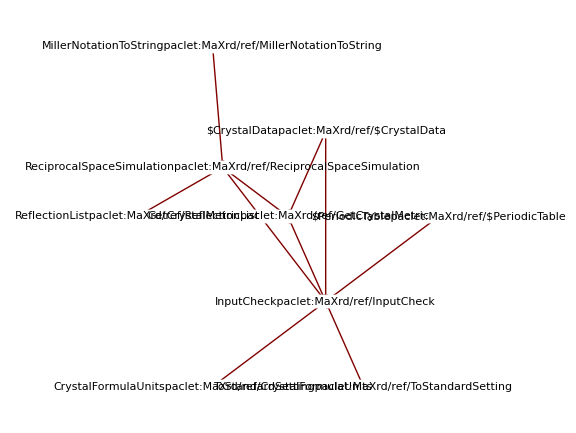

```mathematica
RelatedFunctionsGraph[ReciprocalSpaceSimulation]
```

The essential inputs are the crystal label – which contains the lattice specification – and the orientation details of the plane in reciprocal space. Information on the function syntax:

```mathematica
?ReciprocalSpaceSimulation
```

ReciprocalSpaceSimulation[crystal,{L_1,L_2},origin,d_min] plots a simulation of the reciprocal space of crystal, with L_1 and L_2 defining the layer plane centred at origin and d_min the resolution.
ReciprocalSpaceSimulation[crystal,λ,{L_1,L_2},origin,d_min] plots a simulation of the reciprocal space of crystal at wavelength λ, with L_1 and L_2 defining the layer plane centred at origin and d_min the resolution.

From this we see that the function also requires an origin for the plane, a resolution and wavelength (if not contained along with crystal data). Let us look at some examples:

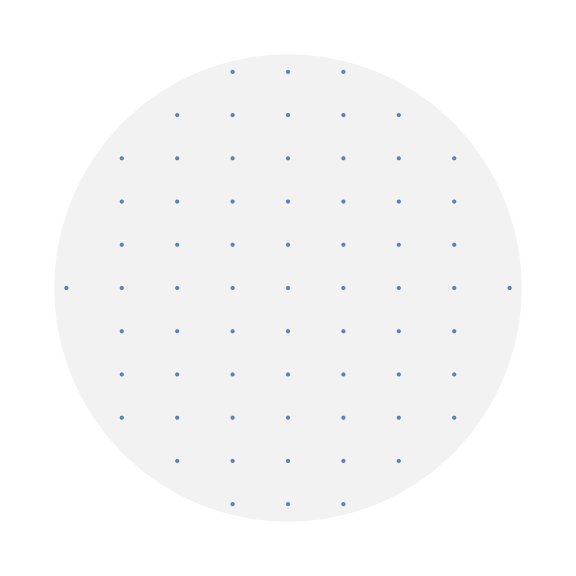

```mathematica
ReciprocalSpaceSimulation[
"LithiumManganesePhosphate",1.54059,
{{1,0,0},{0,0,1}},
{0,2,0},1.12]
(* the (h2l) plane *)
```

The image above shows the (h 2 l) plane of an orthorhombic structure.
Below is an example of a hexagonal structure:

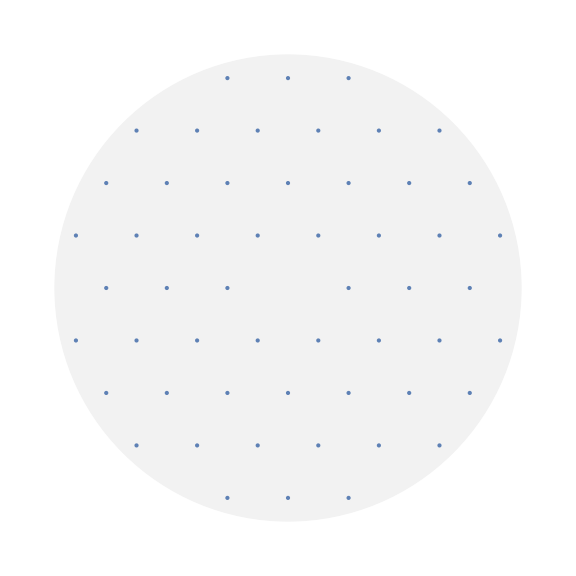

```mathematica
ReciprocalSpaceSimulation[
"Zinc",0.709317,
{{1,0,0},{0,1,0}},
{0,0,0},0.60]
(* the (hk0) plane *)
```

Adjusting the resolution will have the effect of “zooming” in and out. The resolution governs which reflections we are able to see. Note that the indices of the reflections can be read from the tooltips (hover the mouse over any node).

Please see the documentation page for more example of usage.

## Atomic scattering factors

The GetAtomicScatteringFactorspaclet:MaXrd/ref/GetAtomicScatteringFactors function return f_0+f'+ⅈ f'' from either crystal and reflection input or element and sin(θ)/λ input. This function requires sources of coefficients or interpolation functions in order to produce the results, and since the documentation page contains example on use, this tutorial will elaborate on the origin of the source tables included in this package.

Sixteen .dat files are available at ESRF's FTP serverhttp://ftp://ftp.esrf.eu/pub/scisoft//xop2.3/DabaxFiles, with prefix f0 for files regarding the f_0 factor and prefix f1f2 for the f'+f'' factors. After retrieving these (late 2017) they were prepared in a format to be imported by Mathematica when needed.

The data is stored in two different ways: either as coefficients (so-called Cromer–Mann coefficients) to approximate the scattering factor with the function

f^(0)=∑_(i=1) a_i exp(-b_i s^2)+c	where     s≡sin(θ)/λ

where i runs from 1 to 4 or 5, or as data points: {s,f^(0)(s)} in the f0 cases and {E,f'(E),f''(E)} in the f1f2 cases, where s is defined above and E denotes energy. Actually, some files contain more columns, but these are ignored. Energy units are converted to ångströms.

The coefficients method is only available for the f0 case, but some files use the data point method. An overview is given here (third column show valid range; missing means  s<2.5 Å^-1 [truncated]):

f0_CromerMann.dat		coefficients (9 constants)		 s<1.5 Å^-1

f0_EPDL97.dat		data points {s,f^(0)(s)}

f0_InterTables.dat		coefficients (9 constants)		 s<2.0 Å^-1

f0_mf_Kissel.dat		data points {s,f^(0)(s)}

f0_rf_Kissel.dat		data points {s,f^(0)(s)}

f0_WaasKirf.dat		coefficients (11 constants)		 s<6.0 Å^-1

f0_xop.dat			coefficients (11 constants)		?

For completeness, the f1f2 files are:

f1f2_asf_Kissel.dat

f1f2_BrennanCowan.dat

f1f2_Chantler.dat

f1f2_CromerLiberman.dat

f1f2_EPDL97.dat

f1f2_Henke.dat

f1f2_Sasaki.dat

f1f2_Windt.dat

In all cases where data points are used, the Mathematica function Interpolationpaclet:ref/Interpolation was used to generate interpolation functions; one for every data pair within each chemical element. Finally, all the interpolation functions were stored as an association with element symbols as keys. This was saved to an m file with the same name as the dat file.

Organisation scheme for f0 functions (those with data point format):

```mathematica
<|"H"->f0H[λ],"He"->f0He[λ],"Li"->f0Li[λ],…|>
```

Organisation scheme for f1f2 functions:

```mathematica
<|
		"H"->(f1H[#]+ⅈ*f2H[#])&[λ],
		"He"->(f1He[#]+ⅈ*f2He[#])&[λ],
		"Li"->(f1Li[#]+ⅈ*f2Li[#])&[λ],
		…|>
```

where the f* functions are the corresponding interpolation functions generated, which require a wavelength input and return the value of f0, f1 or f2.

The f0 interpolation functions use interpolation order 3, while the f1f2 functions use order 1 (linear). All use the Hermite interpolation method.

Note that for all f0, f1 and f2 interpolation functions the desired scattering factor is obtained with:

```mathematica
sourceName["element"][wavelength]
```

where sourceName denotes one of the associations constructed from any of the dat files storing the information as data points, "element" should be the symbol of a chemical element and the wavelength is in ångströms. A demonstration of this is in order: After using GetAtomicScatteringFactorspaclet:MaXrd/ref/GetAtomicScatteringFactors the first time in a session, the following “hidden” symbols are created:
	MaXrd`Private`$f0
	MaXrd`Private`$f1f2
These associate the file names with the corresponding imported associations.

```mathematica
GetAtomicScatteringFactors["Silicon",{1,1,1},1.541]
```

<|Si→10.7921+0.33034 ⅈ|>

After running the code above, the symbols are created. Let us check this:

```mathematica
Keys/@{MaXrd`Private`$f0,MaXrd`Private`$f1f2}
```

{{WaasmaierKirfel},{CromerLiberman}}

We recognise the default f0 and f1f2 sources. The "WaasmaierKirfel" source contain coefficients:

```mathematica
MaXrd`Private`$f0["WaasmaierKirfel"]["He"]//Normal//TableForm
```

Method→RHF
a1→0.732354
b1→11.5539
a2→0.753896
b2→4.59583
a3→0.283819
b3→1.5463
a4→0.190003
b4→26.464
a5→0.039139
b5→0.377523
c→0.000487

while the "CromerLiberman" source uses data points (as all f1f2 data files):

```mathematica
MaXrd`Private`$f1f2["CromerLiberman"]["Fe"][1.234]
```

-0.0149744+2.22357 ⅈ

## Structure factors

The StructureFactorpaclet:MaXrd/ref/StructureFactor function is written in a way that requires minimal input from the user. Syntax information:

```mathematica
?StructureFactor
```

StructureFactor[crystal,{h,k,l}] calculates the structure factor of the hkl reflection for crystal at wavelength stored in $CrystalData.
StructureFactor[crystal,{h,k,l},λ] calculates the structure factor of the hkl reflection for crystal at wavelength λ.
StructureFactor[crystal,{{h_1,k_1,l_1},{h_2,k_2,l_2},…},λ] calculates the structure factor of the hkl_i reflections for crystal at wavelength λ.

Note that the crystal name/label is required and a list of one or more reflections. The wavelength is necessary if not already contained in along with the crystal in $CrystalDatapaclet:MaXrd/ref/$CrystalData.
StructureFactorpaclet:MaXrd/ref/StructureFactor incorporates several other functions in the package, see the graph below.

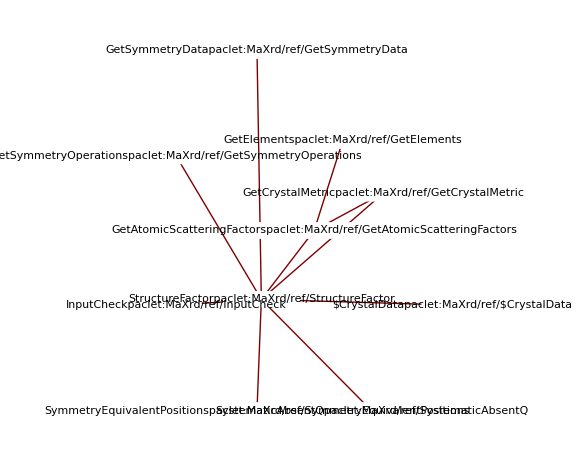

```mathematica
RelatedFunctionsGraph[StructureFactor]
```

There are also some options available:

```mathematica
Options@StructureFactor//TableForm
```

AbsoluteValue→True
Units→True
IgnoreSystematicAbsence→False
Threshold→1.×10^-6
DispersionCorrections→True
f0Source→WaasmaierKirfel
f1f2Source→CromerLiberman
IgnoreIonCharge→True

Details are found on the documentation page. Note the options for specifying which sources to use for obtaining the atomic scattering factor (f=f_0+f'+f''). The available sources are located in:

$UserBaseDirectory ▶ Applications ▶ MaXrd ▶ Core ▶ Data ▶ AtomicScatteringFactor

Which in the current version include:

```mathematica
FileBaseName/@FileNames["*.m",FileNameJoin[
{$MaXrdPath,"Core","Data","AtomicScatteringFactor"}]]//TableForm
```

CromerMann
EPDL97
InternationalTablesC(3rd)
Kissel
Kissel(modified)
WaasmaierKirfel
XOP(2.1)

The sources for the anomalous corrections are contained in a subfolder:

$UserBaseDirectory ▶ Applications ▶ MaXrd ▶ Core ▶ Data ▶ AtomicScatteringFactor ▶ AnomalousCorrections

```mathematica
FileBaseName/@FileNames["*.m",FileNameJoin[
{$MaXrdPath,"Core","Data","AtomicScatteringFactor","AnomalousCorrections"}]]//TableForm
```

BrennanCowan
Chantler
CromerLiberman
EPDL97
Henke
Kissel
Sasaki
Windt
xraylib

Here are some quick demonstartions for the crystals gallium arsenide and germanium (the wavelength corresponds to Cu Kα_1 radiation):

```mathematica
StructureFactor["GalliumArsenide",{4,2,2},1.54059]
```

{119.825,3.01254 °}

```mathematica
StructureFactor["Germanium",{3,1,1},1.54059]
```

{114.924,-177.618 °}

By default, the modulus and phase are outputted in pairs: {|F_hkl|,ϕ_hkl}. Complex numbers can be used instead:

```mathematica
StructureFactor["Germanium",{3,1,1},1.54059,"AbsoluteValue"->False]
```

-114.824-4.77555 ⅈ

Please see the documentation page for more example of usage and elaboration on the options.

## Unit cell transformation

This package includes the function UnitCellTransformationpaclet:MaXrd/ref/UnitCellTransformation that transforms entries in $CrystalDatapaclet:MaXrd/ref/$CrystalData among alternative settings of the same space group. In this example we will look at how the metric is transformed, and will be demonstrating this on the crystal ferrocene.

First import the crystal data from a .cif file (in the package)

```mathematica
file=FileNameJoin[{$MaXrdPath,"ExampleFiles","CIF","Ferrocene.cif"}];
ImportCrystalData[file]
```

{ChemicalFormula→C_10H_10Fe,FormulaUnits→2,SpaceGroup→P2_1/n,LatticeParameters→<|a→5.9285 Å,b→7.612 Å,c→9.041 Å,α→90 °,β→93.156 °,γ→90 °|>,Wavelength→0.69804 Å,AtomData→{«11»}}

Ferrocene has the monoclinic space group P 2_1/n:

```mathematica
$CrystalData["Ferrocene","SpaceGroup"]
```

P2_1/n

It is currently not in the standard setting (which is P 2_1/c). Let us now look up the setting(s) specifying this particualar space group.

```mathematica
$GroupSymbolRedirect["P2_1/n"]["Setting"]
```

<|UniqueAxis→b,CellChoice→2|>

There may be several attributes, such as cell origin, cell choice, axis permutation, centring and so forth. In this case, there are only two setting parameters to fiddle with. We see that the b-axis is the unique axis, which is the standard choice, but the cell choice is set to 2 instead of 1.

Let us transform the cell so that the a-axis becomes the uniqe axis (the axis with a corresponding angle different from 90 °). We can either use the International Tables for Crystallography, volume A or $TransformationMatricespaclet:MaXrd/ref/$TransformationMatrices:

The transformation matrix that changes unique axis b to a:

```mathematica
P=$TransformationMatrices["UniqueAxisB_to_A"];
P//MatrixForm
```

(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0)

We need the current metric of the crystal, G:

```mathematica
G=GetCrystalMetric["Ferrocene"]
```

{{35.1471,0,-2.95091},{0,57.9425,0},{-2.95091,0,81.7397}}

Transforming to the new metric, G_2:

```mathematica
G2=Transpose[P].G.P;
```

Notice how the lattice parameters have been permuted:

```mathematica
GetLatticeParameters[G]
GetLatticeParameters[G2]
```

{5.9285 Å,7.612 Å,9.041 Å,90 °,93.156 °,90 °}

{7.612 Å,9.041 Å,5.9285 Å,93.156 °,90 °,90 °}

If we wanted to change the cell choice at the same time, we would simply multiply the two transformation matrices together to a form another matrix P=P_1 P_2 to be used in G_2=P^T G P.

We conclude this example with a demonstration of UnitCellTransformationpaclet:MaXrd/ref/UnitCellTransformation that performs the same transformation of ferrocene as we did «manually»:

```mathematica
UnitCellTransformation["Ferrocene","UniqueAxis"->"a"]
```

{ChemicalFormula→C_10H_10Fe,FormulaUnits→2,SpaceGroup→P 21/n 1 1,LatticeParameters→<|a→7.612 Å,b→9.041 Å,c→5.9285 Å,α→93.156 °,β→90 °,γ→90 °|>,Wavelength→0.69804 Å,AtomData→{«11»}}

You may notice how the new space group symbol is P 2_1/n 1 1. If the symbol is ambiguous, full Hermann–Mauguin symbols are used for non-standard settings.

The function UnitCellTransformationpaclet:MaXrd/ref/UnitCellTransformation also transforms the fractional coordinates and the ADPs (atomic displacement parameters).